```mathematica
SetDirectory[NotebookDirectory[]<>"../pics"]
```

/home/jam/Kuweta/mma_lessons/pics

## Simple example

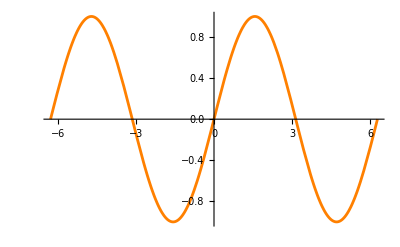

```mathematica
simplePlot=Plot[Sin[x],{x,-2 Pi, 2 Pi}, PlotStyle -> Orange]
```

```mathematica
Export["04-plot-simple-example.pdf",simplePlot]
```

04-plot-simple-example.pdf

## Range specification

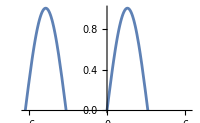

```mathematica
xRangeSpecPlot=Plot[Sin[x],{x,-2 Pi, 2 Pi},  ImageSize->200, PlotRange->{0,1}]
```

```mathematica
Export["04-plot-x-range-example.pdf",xRangeSpecPlot]
```

04-plot-x-range-example.pdf

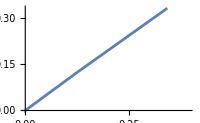

```mathematica
xyRangeSpecPlot=Plot[Sin[x],{x,-2 Pi, 2 Pi}, ImageSize->200, PlotRange->{{0,π/8},{0,1/3}} ]
```

```mathematica
Export["04-plot-xy-range-example.pdf",xyRangeSpecPlot]
```

04-plot-xy-range-example.pdf

## Frame and axes

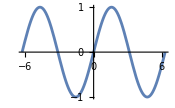

```mathematica
xAxesPlot=Plot[Sin[x],{x,-2 Pi, 2 Pi}, ImageSize->175,Axes->{True,False}]
```

```mathematica
Export["04-plot-x-axes-example.pdf",xAxesPlot]
```

04-plot-x-axes-example.pdf

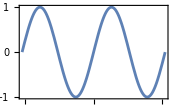

```mathematica
framePlot=Plot[Sin[x],{x,-2 Pi, 2 Pi},ImageSize->175,Frame->True,Axes->False]
```

```mathematica
Export["04-plot-frame-example.pdf",framePlot]
```

04-plot-frame-example.pdf

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

## Ticks

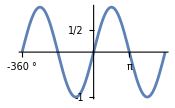

```mathematica
ticksPlot=Plot[Sin[x],{x,- 2 Pi, 2 Pi},ImageSize->175,
Ticks->{
{{-2Pi,-360°}, {-Pi,-180°}, 0,Pi,2Pi,3Pi},
{-1,-1/2,0,1/2,1}
}
]
```

```mathematica
Export["04-plot-ticks.pdf",ticksPlot]
```

04-plot-ticks.pdf

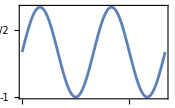

```mathematica
frameTicksPlot=Plot[Sin[x],{x,-2 Pi,2 Pi},ImageSize->175,
Frame->True,
FrameTicks->{
{{-2Pi,-360°}, {-Pi,-180°}, 0,Pi,2Pi,3Pi},
{-1,-1/2,0,1/2,1}
}
]
```

```mathematica
Export["04-plot-frameticks.pdf",frameTicksPlot]
```

04-plot-frameticks.pdf

## Two functions in one plot

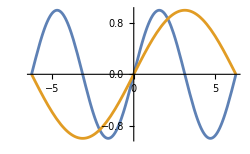

```mathematica
twoPlot=Plot[{Sin[x],Sin[x/2]},{x,-2 Pi,2 Pi}, ImageSize->250]
```

```mathematica
Export["04-plot-two-fun-example.pdf",twoPlot]
```

04-plot-two-fun-example.pdf

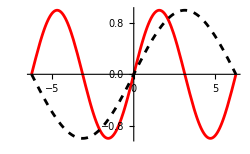

```mathematica
twoStylesPlot=Plot[{Sin[x],Sin[x/2]},{x,-2 Pi,2 Pi}, ImageSize->250,PlotStyle->{Directive[Red],Directive[Black,Dashed]}]
```

```mathematica
Export["04-plot-two-styles-example.pdf",twoStylesPlot]
```

04-plot-two-styles-example.pdf

## Full example

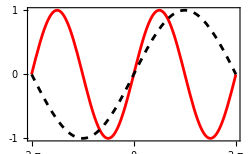

```mathematica
plotFullExample=Plot[{Sin[x],Sin[x/2]},{x,-2Pi,2Pi},
PlotRange->{{-2Pi,2Pi},{-1,1}},
PlotStyle->{Red,Directive[Black,Dashed]},
Axes->True,
ImageSize->250,
FrameTicks->{
{{-1,0,1},{-1,0,1}},
{{-2Pi,-Pi,0,Pi,2Pi},{-2Pi,-Pi,0,Pi,2Pi}}
},
Frame->True,
LabelStyle->Directive[12,Bold,Black]
]
```

```mathematica
Export["04-plot-full-example.pdf",plotFullExample]
```

04-plot-full-example.pdf

## Evaluation points

```mathematica
$PlotTheme=.
```

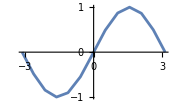

```mathematica
plotPointsExample=Plot[Sin[x],{x,-Pi, Pi}, ImageSize->175, PlotPoints->4,MaxRecursion->2]
```

```mathematica
Export["04-plot-points-example.pdf",plotPointsExample];
```

## Discrete plot

```mathematica
$PlotTheme=.
```

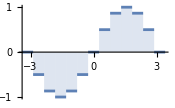

```mathematica
discretePlotExample=DiscretePlot[Sin[x],{x,-Pi,Pi,Pi/6},ExtentSize->Full, ImageSize->175]
```

```mathematica
Export["04-discrete-plot-example.pdf",discretePlotExample]
```

04-discrete-plot-example.pdf

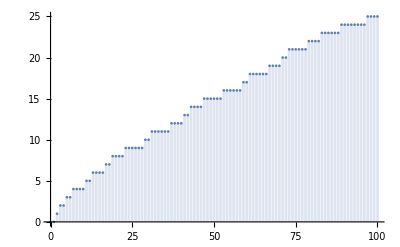

```mathematica
discretePlotPrimePi=DiscretePlot[PrimePi[x],{x,0,100}]
```

```mathematica
Export["04-discrete-plot-primepi.pdf",discretePlotPrimePi]
```

04-discrete-plot-primepi.pdf

## Size of the graphics

```mathematica
$PlotTheme=.
```

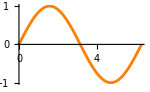

```mathematica
Plot[Sin[x],{x,0,2 Pi},ImageSize->150,PlotStyle->Orange]
```

```mathematica
Export["04-plot-sin-small.pdf",%];
```

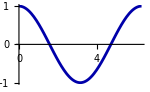

```mathematica
Plot[Cos[x],{x,0,2 Pi},ImageSize->150,PlotStyle->Darker[Blue]]
```

```mathematica
Export["04-plot-cos-small.pdf",%];
```

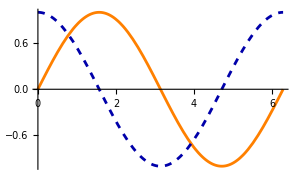

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},ImageSize->300,PlotStyle->{Orange,Directive[Darker[Blue], Dashed]}]
```

```mathematica
Export["04-plot-large.pdf",%];
```

```mathematica
Table[
Export[NotebookDirectory[]<>"pics/04-plot-theme-"<>ToString[t]<>".pdf",
Plot[Sin[x],{x,0,2 Pi}, PlotTheme->t,ImageSize->200,PlotLabel->t]
],{t,{"Classic", "Scientific", "Web","Buissines"}}
]
```

{/home/jam/Kuweta/mma_lessons/code/pics/04-plot-theme-Classic.pdf,/home/jam/Kuweta/mma_lessons/code/pics/04-plot-theme-Scientific.pdf,/home/jam/Kuweta/mma_lessons/code/pics/04-plot-theme-Web.pdf,/home/jam/Kuweta/mma_lessons/code/pics/04-plot-theme-Buissines.pdf}

```mathematica
$PlotTheme="Scientific"
```

Scientific

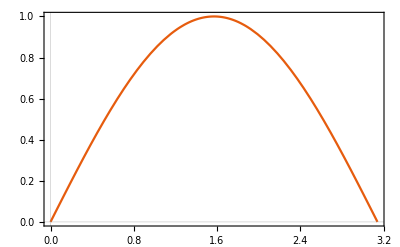

```mathematica
Plot[Sin[x],{x,0, Pi}]
```

## Using PlotTheme

```mathematica
?PlotTheme
```

```mathematica
Table[
Export[NotebookDirectory[]<>"pics/04-plot-theme-"<>ToString[t]<>".pdf",
Plot[Sin[x],{x,0,2 Pi}, PlotTheme->t, ImageSize->175,PlotLabel->t]
],{t,{"Classic", "Scientific", "Web","Buissines"}}
]
```